# Inflationary Era For Gauss-Bonnet Toy-Models.

## Designation Of Initial Scalar Function And Continuity Equation:

Firstly, the scalar potential is designated. Parameter Λ is an unspecified for the time being constant with mass dimensions [Λ]=4. It can be dimensionless if Λ->ΛMp^4 or Λ/κ^4. Similarly, α is an additional dimensionless parameter, it can be replaced with unity for simplicity. The same applies to exponent n.
Here, the approximated continuity equation is designated for the case of cT^2=1 according to arxiv:0412126 and arxiv:2003.13724. The framework is selected such that the Gauss0Bonnet scalar coupling function is directly derivable from the continuity equation (being a second order differential equation) once the scalar potential is designated. For clarity, a Ricci coupling is introduced in order to account for the non-minimally coupled case however the example showcased, taken from arXiv 2001.07012, is studied in the minimal case.

```mathematica
V[φ_]:=Λ Tanh[κ φ/Sqrt[6α]]^(2n)
f[φ_]:=1
difeq=V'[φ]+κ^2V[φ]D[ξ0[φ],φ]/D[ξ0[φ],{φ,2}]-2V[φ]D[f[φ],φ];
```

### Solution of the differential equation:

```mathematica
sol1=DSolve[difeq==0,ξ0[φ],φ]
```

{{ξ0[φ]→C[2]+∫_1^φ ⅇ^(-(3 α Cosh[(√(2/3) κ K[1])/(√α)])/(4 n)) C[1]ⅆK[1]}}

## Designation Of Auxiliary Parameters

The Gauss Bonnet scalar coupling function is specified. Since the continuity equation is a second order differential with respect to ξ, its form is not always functional.

```mathematica
ξ[φ_]:=ξ0[φ]/.sol1[[1]]/.{C[1]->λ,C[2]->0}
```

In consequence, the rest equations of motion along with certain auxiliary parameters and the observed indices are specified. Firstly, the equations of motion are the same as in the canonical scalar field inflation since it is assumed that string corrective terms are negligible, a valid assumption as it will be proven subsequently. The auxiliary parameters concerning string corrections are taken from the previous two references. Furthermore, the slow-roll indices along with the observed indices are simplified greatly (in fact the last three slow-roll indices are negligible most of the times, hardly relevant whereas the tensor to scalar ratio is simplified greatly in the case of Qe being subleading and CA being unity). The validoty of the approximations is examined in the end however  if even a single one is violated, for instance if CA<<1, the original forms from the previous references must be used. A plethora of models studied suggest that the aforementioned assumptions are indeed valid and only break down in the case of extra string corrections. Also, in the non-miminally coupled case, Hdot may be changed to a more suitable form. A throrough analysis is perfomed on arXiv:2007.02309 on the possible approximations on the equations of motion.

```mathematica
H2[φ_]:=κ^2V[φ]/(3f[φ])
H[φ_]:=Sqrt[H2[φ]]
φdot[φ_]:=H[φ] D[ξ[φ],φ]/D[ξ[φ],{φ,2}]
Hdot[φ_]:=-(κ φdot[φ])^2/(2f[φ])
Qa[φ_]:=-8D[ξ[φ],φ]φdot[φ]H2[φ]
Qt[φ_]:=f[φ]/κ^2-8D[ξ[φ],φ]φdot[φ]H[φ]
Qe[φ_]:=-32D[ξ[φ],φ]φdot[φ]Hdot[φ]
CA[φ_]:=Sqrt[1+κ^2(D[f[φ],φ]φdot+κ^2Qa[φ])Qe[φ]/(2κ^4Qt[φ]φdot[φ]^2+3(D[f[φ],φ]φdot[φ]+κ^2Qa[φ]^2))]
E0[φ_]:=f[φ]/(κ φdot[φ])^2*(φdot[φ]^2+(3(D[f[φ],φ]φdot[φ]+κ^2Qa[φ])^2)/(2κ^4Qt[φ]))
ε1[φ_]:=-Hdot[φ]/H2[φ]
ε2[φ_]:=1-ε1[φ]-D[ξ[φ],φ]D[ξ[φ],{φ,3}]/D[ξ[φ],{φ,2}]^2
ε3[φ_]:=D[f[φ],φ]φdot[φ]/(2H[φ]f[φ])
ε4[φ_]:=D[E0[φ],φ]φdot[φ]/(2H[φ]E0[φ])
ε5[φ_]:=(D[f[φ],φ]φdot[φ]+κ^2Qa[φ])/(2κ^2H[φ]Qt[φ])
ε6[φ_]:=D[Qt[φ],φ]φdot[φ]/(2H[φ]Qt[φ])
ns[φ_]:=1-2(2ε1[φ]+ε2[φ]-ε3[φ])//Simplify
r[φ_]:=16Abs[(ε1[φ]+ε3[φ])f[φ]/(κ^2Qt[φ])]//Simplify
nt[φ_]:=-2(ε1[φ]+ε3[φ])//Simplify
```

In this case, the approximated forms of the observed indices are used. This is a valid assumption as proven below. Note that in the last line, the tensor spectral index takes ε3 as an input instead of ε6. This is valid only if string corrections are indeed negligible, otherwise ε6 must be used. The numerical values at the end suggest whether this decision is right or wrong. Also, it is always negative, or blue shifted!

## Derivation Of The Final Value Of The Scalar Field

The ending stage of the inflationary era is evaliated roughly when the first slow-roll index becomes of order 1. There may exist possible values which meet such condition. If more values are realised, simply pick one (obviously real).

```mathematica
sol2=Solve[ε1[φ]==1,φ]
φf=φ/.sol2[[3]]/.C[1]->0;
```

{{φ→ConditionalExpression[(√(3/2) √α (-ArcSinh[(2 n)/(√3 √α)]+2 ⅈ π C[1]))/κ,C[1]∈ℤ]},{φ→ConditionalExpression[(√(3/2) √α (ⅈ π-ArcSinh[(2 n)/(√3 √α)]+2 ⅈ π C[1]))/κ,C[1]∈ℤ]},{φ→ConditionalExpression[(√(3/2) √α (ArcSinh[(2 n)/(√3 √α)]+2 ⅈ π C[1]))/κ,C[1]∈ℤ]},{φ→ConditionalExpression[(√(3/2) √α (ⅈ π+ArcSinh[(2 n)/(√3 √α)]+2 ⅈ π C[1]))/κ,C[1]∈ℤ]}}

## Derivation Of The Initial Value Of The Scalar Field

With the final value of the scalar field chosen, the initial value during the first horizon crossing can be evaluated easily by inverting the e-folding number. Caution is needed because in certain cases, Mathematica cannot find the form of sol3. This occurs in many instances where the expression contains logarithms. In orfer to proceed, one may need to write sol3 by hand, using logarithmic identities for sums.

```mathematica
int[φ_]:=Integrate[D[ξ[φ],{φ,2}]/D[ξ[φ],φ]//Simplify,φ]
A=int[φ]/.φ->φl;
B=int[φ]/.φ->φk;
efolds=A-B//Simplify;
Solve[N0==efolds,φk]
sol3=Normal[%,ConditionalExpression];
φi=φk/.sol3[[2]]/.{C[1]->0,φl->φf};
```

{{φk→ConditionalExpression[(√(3/2) √α (-ArcCosh[(4 n N0+3 α Cosh[(√(2/3) κ φl)/(√α)])/(3 α)]+2 ⅈ π C[1]))/κ,C[1]∈ℤ]},{φk→ConditionalExpression[(√(3/2) √α (ArcCosh[(4 n N0+3 α Cosh[(√(2/3) κ φl)/(√α)])/(3 α)]+2 ⅈ π C[1]))/κ,C[1]∈ℤ]}}

## Evaluation Of The Observed Indices/Results

Results can be extracted by designating all free parameters of the model. For numerical purposes, integers have been written with . so as to facilitate the code.

```mathematica
κ=1.;Λ=1.;λ=1.;N0=60.;α=1.;n=1.;
N[φi]
N[φf]
N[ns[φ]/.φ->φi]
N[r[φ]/.φ->φi]
N[nt[φ]/.φ->φi]
```

6.23891

1.20839

0.966885

0.00321008

-0.00040126

### Slow-Roll Indices

A quick look at the order of each slow-roll index indicates whether the approximations imposed both on the equations of motion and on subsequent elements such as the observed indices are valid.

```mathematica
N[ε1[φ]/.φ->φi]
N[ε2[φ]/.φ->φi]
N[ε4[φ]/.φ->φi]
N[ε5[φ]/.φ->φi]
N[ε6[φ]/.φ->φi]
```

0.00020063

0.0161562

4.44788×10^-18

7.2574×10^-29

7.3732×10^-29

## Validity Of The Approximations Imposed

The results are shown here all together however in most cases, only comparisons in pairs are needed to be ascertained.

### Slow-Roll Conditions

```mathematica
N[Hdot[φ]/.φ->φi]
N[H2[φ]/.φ->φi]

N[φdot[φ]^2/.φ->φi]
N[V[φi]]

N[D[φdot[φ],φ]φdot[φ]/.φ->φi]
N[H[φ]φdot[φ]/.φ->φi]
```

-0.0000652559

0.325255

0.000130512

0.975766

-0.000105263

-0.00651534

### 1st Equation Of Motion

```mathematica
N[24D[ξ[φ],φ]φdot[φ]H[φ]^3/.φ->φi]
N[V[φi]]
```

-1.41631×10^-28

0.975766

### 2nd Equation Of Motion

```mathematica
N[16D[ξ[φ],φ]φdot[φ]H[φ]Hdot[φ]/.φ->φi]
N[Hdot[φ]/.φ->φi]
```

1.89435×10^-32

-0.0000652559

### 3rd Equation Of Motion

```mathematica
N[24D[ξ[φ],φ]H2[φ]^2/.φ->φi]
N[V'[φ]/.φ->φi]
```

7.0704×10^-27

0.019546

### Approximations On Tensor-To-Scalar Ratio

```mathematica
N[Qe[φ]/(4H[φ])/.φ->φi]
N[ε1[φ]/.φ->φi]
N[CA[φ]/.φ->φi]
```

-2.9121×10^-32

0.00020063

1.

## Contour Plots

For illustrative purposes,  the contour plot was chosen for the two observed indices which have either been directly measured or have an upper bound. Several cases are shown. In most cases, the decisive factor is the e-folding number, thus rendering the plots tricial.

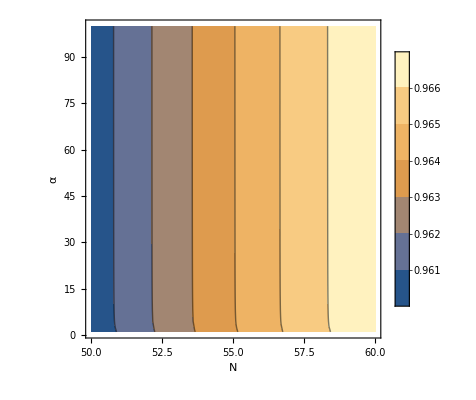

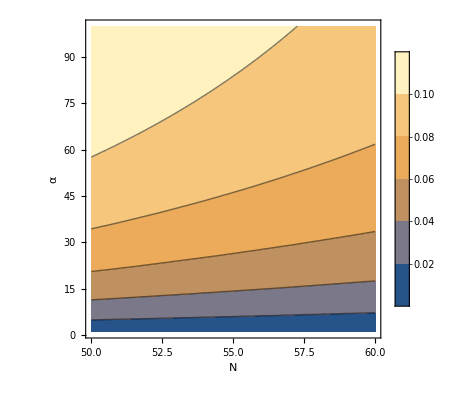

```mathematica
Clear[N0];Clear[α];
ContourPlot[Evaluate[ns[φ]/.φ->φi],{N0,50,60},{α,1,100},FrameLabel->{"N","α"},PlotLegends->True]
ContourPlot[Evaluate[r[φ]/.φ->φi],{N0,50,60},{α,1,100},FrameLabel->{"N","α"},PlotLegends->True]
```

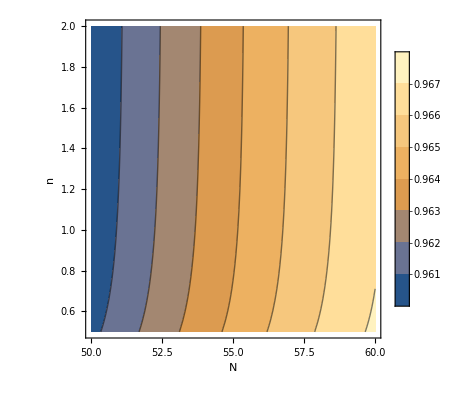

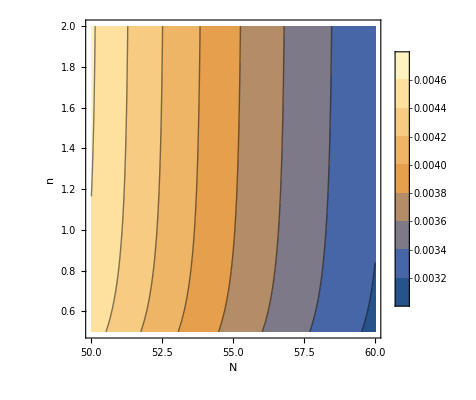

```mathematica
Clear[N0];Clear[n]; α=1;
ContourPlot[Evaluate[ns[φ]/.φ->φi],{N0,50,60},{n,0.5,2},FrameLabel->{"N","n"},PlotLegends->True]
ContourPlot[Evaluate[r[φ]/.φ->φi],{N0,50,60},{n,0.5,2},FrameLabel->{"N","n"},PlotLegends->True]
```

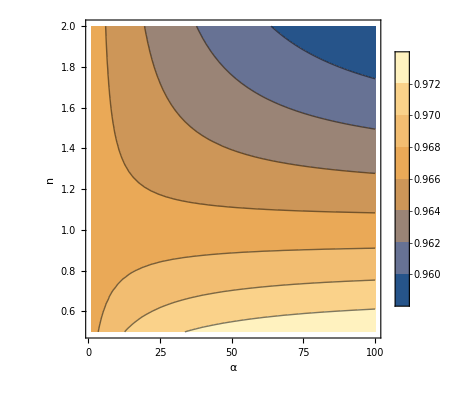

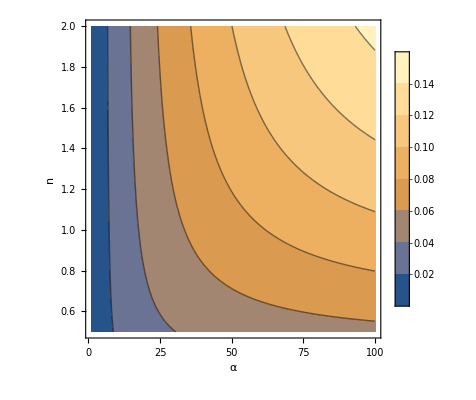

```mathematica
N0=60;Clear[n]; Clear[α];
ContourPlot[Evaluate[ns[φ]/.φ->φi],{α,1,100},{n,0.5,2},FrameLabel->{"α","n"},PlotLegends->True]
ContourPlot[Evaluate[r[φ]/.φ->φi],{α,1,100},{n,0.5,2},FrameLabel->{"α","n"},PlotLegends->True]
```